```mathematica
(*This Mathematica file can be used to reproduce Fig.3 reported in Phys.Rev.A 98,063837 (2018). The variable "steadystate" computes analytically the steady state of the equations mentioned in Appendix A. The symbols has the following meanings, 
γ= linewidth of the atoms, N1= number of atoms,
g= light-matter coupling, δ = pump rate of the atoms, 
κ= linewidth of the cavity *)



Clear["Global`*"]
steadystate= Solve[{ⅈ g N1 Y2-ⅈ g N1 Y3 - κ(Y1-1)==0, -ⅈ g *0.5*(1-Y4)-ⅈ g Y4 Y1-(N1-1)ⅈ g Y5- (κ/2 + γ/2 + δ/2)Y2==0,ⅈ g *0.5*(1-Y4)+ⅈ g Y4 Y1+(N1-1)ⅈ g Y5- (κ/2 + γ/2 + δ/2)Y3==0, -2 ⅈ g Y2+2 ⅈ g Y3-γ(1+Y4)+δ(1-Y4)==0,ⅈ g Y4 Y2-ⅈ g Y4 Y3-(γ+δ)Y5==0},{Y1,Y2,Y3,Y4,Y5}];

ss1= Y1/.steadystate[[1]];
ss2= Y2/.steadystate[[1]];
ss3= Y3/.steadystate[[1]];
ss4= Y4/.steadystate[[1]];

(*The linewidth is calculated using the filter cavity. Before calculating the spectrum, we specify some of the parameters, and compute the spectrum numerically. Here, 
G is coupling of the filter cavity with the cavity of interest, 
and α is the linewidth of the filter cavity. It is necessary that the linewidth of the filter cavity is less than the linewidth of the emitted signal *)
γ=0.001 ;
g= 2.41;
N1=10^6;
κ= 160*10^3;
α= 10^-11;
G= 10^-8;
fSpace[min_,max_,steps_,f_: Log]:=InverseFunction[f]/@Range[f@min,f@max,(f@max-f@min)/(steps-1)]
del=fSpace[10^(-4), 10^3, 151];
check={};
count= 1;
fwhm=Table[0,{i,Length[del]}];
For[l1=1,l1≤Length[del],l1++,
δ=del[[l1]];

(*result2 solves the second-order mean-field equations shown in Appendix C of the article *)
result2= Solve[{ⅈ G X2-ⅈ G X3- α(X1-1)==0, ⅈ g N1 X4-ⅈ G ss1-ⅈ wb X2+ⅈ G X1- (α/2 + κ/2)X2==0, ⅈ G ss1+ⅈ wb X3-ⅈ G X1-ⅈ g N1 X5- (α/2 + κ/2)X3==0, -ⅈ G ss2-ⅈ wb X4-ⅈ g ss4 X2- (α/2 + γ/2 + δ/2)X4==0,  ⅈ G ss3+ⅈ g ss4 X3+ⅈ wb X5- (α/2 + γ/2 + δ/2)X5==0},{X1,X2,X3,X4,X5}];

ans= X1/.result2;
photon=FullSimplify[ans];

(* Here it calculates the number of photons when the resonance frequency of the filter cavity is zero*)
maxphoton=photon/.{wb->0};
max=Abs[maxphoton]-1;

(*Here it computes the frequency of the filter cavity where the photon number drops by half, which is basically the FWHM of the emitted signal. Refer to Phys.Rev.A 98, 063837 (2018) for discussion on filter cavity and calculation of the emitted spectrum. *)
final= Solve[{(Abs[photon]-1)==max/2},wb];

min= Min[Abs[Im[wb/.final]]];

For [l2=1,l2≤Length[final],l2++,

present= Abs[Im[wb/.final[[l2]]]];
If[present==min,
fwhm[[l1]]=2* Abs[Re[wb/.final[[l2]]]];
]
]
]
```

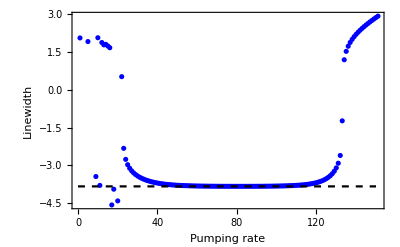

```mathematica
(* Visualizing Fig. 3 *)
p1=ListPlot[Log10[fwhm], Frame->True,  PlotStyle->Blue, FrameLabel->{Pumping rate,Linewidth}];
p2=Plot[Log10[(4*g*g)/κ],{x,0,150},Frame->True, PlotStyle->{Black, Dashed}, FrameLabel->{Pumping rate,Linewidth}]; (* This calculates the Purcell rate for comparison *)
Show[{p1,p2}, Axes->None]
```